# Ecological Models

## Predator - Prey system

```mathematica
(*Dynamical system for a prey(x)-predator(y) system*)
de1:=x'=a*x-b*x*y
de2:=y'=-c*y+d*x*y
```

```mathematica
(*Define the differential equations in terms of their variables*)
Prey[a_,b_]=de1;
Predator[c_,d_]=de2;
```

```mathematica
(*Plot the prey-predator dynamical system*)
(*Assumed a, b, c, d > 0*)
(*In this system, there is no assumption on the Prey's food source -> assumed unlimited*)
Manipulate[StreamPlot[{Prey[a,b],Predator[c,d]},{x,0,10},{y,0,10},FrameLabel->{"Prey","Predator"}],{a,0,10,Appearance->"Open"},{b,0,10,Appearance->"Open"},{c,0,10,Appearance->"Open"},{d,0,10,Appearance->"Open"}]
```

## Application to Cosmology

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
dex:=x'=-3*x*(1+wx)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

{{x→0,z→0},{x→3/q,z→-(3 (1+wx))/q}}

```mathematica
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,2}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(-3-3 wx-q z | -q x
q z | -3+q x)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0) | (-3 (1+wx) | 0
0 | -3) | (-3
3 (-1-wx)) | (0 | 1
1 | 0)
(3/q
-(3 (1+wx))/q) | (0 | -3
-3 (1+wx) | 0) | (-3 √(1+wx)
3 √(1+wx)) | (1/(√(1+wx)) | 1
-1/(√(1+wx)) | 1)

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_]=dex;
DM[q_]=dez;
```

```mathematica
Manipulate[StreamPlot[{DE[wx,q],DM[q]},{x,0,1},{z,0,1},FrameLabel->{"x","z"}],{q,0,20,Appearance->"Open"},{wx,-2,2,Appearance->"Open"}]
```

## Modified Energy Density System

### x - z Phase Space

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
dex:=x'=-3*x*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

{{x→3/q,z→-(3 (q+q wx+3 ϵ))/q^2},{x→0,z→0},{x→-(1+wx)/ϵ,z→0}}

```mathematica
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(-3-3 wx-q z-6 x ϵ | -q x
q z | -3+q x)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(3/q
-(3 (q+q wx+3 ϵ))/q^2) | (-(9 ϵ)/q | -3
-(3 (q+q wx+3 ϵ))/q | 0) | ((3 (-3 q ϵ-q √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)))/(2 q^2)
(3 (-3 q ϵ+q √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)))/(2 q^2)) | (-(-3 ϵ-√(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2))/(2 (q+q wx+3 ϵ)) | 1
-(-3 ϵ+√(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2))/(2 (q+q wx+3 ϵ)) | 1)
(0
0) | (-3 (1+wx) | 0
0 | -3) | (-3
3 (-1-wx)) | (0 | 1
1 | 0)
(-(1+wx)/ϵ
0) | (3 (1+wx) | (q (1+wx))/ϵ
0 | -3-(q (1+wx))/ϵ) | (3 (1+wx)
-(q+q wx+3 ϵ)/ϵ) | (1 | 0
-(q (1+wx))/(q+q wx+6 ϵ+3 wx ϵ) | 1)

```mathematica
(*Find condition for first fixed point to be complex*)
wxCond=Solve[4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2==0,{q,ϵ,wx}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{wx→-(2 q+3 ϵ)^2/(4 q^2)},{q→0,ϵ→0}}

```mathematica
wxCondition=wx/.wxCond[[1]]
```

-(2 q+3 ϵ)^2/(4 q^2)

```mathematica
(*Maximum value wx can be for positive values of ϵ and q -> Fig. 9a*)
wxMax1=wxCondition/.{ϵ->0.01,q->.1}
```

-1.3225

```mathematica
(*Maximum value wx can be for positive q and negative ϵ to reproduce Fig. 9b*)
wxMax2=wxCondition/.{ϵ->-0.25,q->1}
```

-0.390625

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=dex;
DM[q_]=dez;
```

```mathematica
Manipulate[StreamPlot[{DE[wx,q,ϵ],DM[q]},{x,0,5},{z,0,3},FrameLabel->{"x","z"}],{q,0,20,Appearance->"Open"},{wx,-10,10,Appearance->"Open"},{ϵ,-2,2,Appearance->"Open"}]
```

### x - y - z Phase Space

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1:=x'=-3*y*x*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(x+z+3*wx*x+3*ϵ*x^2)
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,z→-x-3 wx x-3 x^2 ϵ},{x→0,y→0,z→0},{x→3/q,y→-(√(-q wx-3 ϵ))/q,z→-(3 (q+q wx+3 ϵ))/q^2},{x→3/q,y→(√(-q wx-3 ϵ))/q,z→-(3 (q+q wx+3 ϵ))/q^2},{x→(-1-wx)/ϵ,y→-(√(-1-wx))/(√3 √ϵ),z→0},{x→(-1-wx)/ϵ,y→(√(-1-wx))/(√3 √ϵ),z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,6}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(-y (3+3 wx+q z+6 x ϵ) | -x (3+3 wx+q z+3 x ϵ) | -q x y
1/6 (-1-3 wx-6 x ϵ) | -2 y | -1/6
q y z | (-3+q x) z | (-3+q x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,6}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0
-x-3 wx x-3 x^2 ϵ) | (0 | x (3 wx (-1+q x)-3 (1+x ϵ)+q x (1+3 x ϵ)) | 0
1/6 (-1-3 wx-6 x ϵ) | 0 | -1/6
0 | -x (-3+q x) (1+3 wx+3 x ϵ) | 0) | (0
-(ⅈ √x √(-wx-3 wx^2+q wx x+3 q wx^2 x-4 x ϵ-9 wx x ϵ+2 q x^2 ϵ+9 q wx x^2 ϵ-6 x^2 ϵ^2+6 q x^3 ϵ^2))/(√2)
(ⅈ √x √(-wx-3 wx^2+q wx x+3 q wx^2 x-4 x ϵ-9 wx x ϵ+2 q x^2 ϵ+9 q wx x^2 ϵ-6 x^2 ϵ^2+6 q x^3 ϵ^2))/(√2)) | (-1/(1+3 wx+6 x ϵ) | 0 | 1
-(-3-3 wx+q x+3 q wx x-3 x ϵ+3 q x^2 ϵ)/((-3+q x) (1+3 wx+3 x ϵ)) | (ⅈ √(-wx-3 wx^2+q wx x+3 q wx^2 x-4 x ϵ-9 wx x ϵ+2 q x^2 ϵ+9 q wx x^2 ϵ-6 x^2 ϵ^2+6 q x^3 ϵ^2))/(√2 √x (-3+q x) (1+3 wx+3 x ϵ)) | 1
-(-3-3 wx+q x+3 q wx x-3 x ϵ+3 q x^2 ϵ)/((-3+q x) (1+3 wx+3 x ϵ)) | -(ⅈ √(-wx-3 wx^2+q wx x+3 q wx^2 x-4 x ϵ-9 wx x ϵ+2 q x^2 ϵ+9 q wx x^2 ϵ-6 x^2 ϵ^2+6 q x^3 ϵ^2))/(√2 √x (-3+q x) (1+3 wx+3 x ϵ)) | 1)
(0
0
0) | (0 | 0 | 0
1/6 (-1-3 wx) | 0 | -1/6
0 | 0 | 0) | (0
0
0) | (-1/(1+3 wx) | 0 | 1
0 | 1 | 0
0 | 0 | 0)
(3/q
-(√(-q wx-3 ϵ))/q
-(3 (q+q wx+3 ϵ))/q^2) | ((9 √(-q wx-3 ϵ) ϵ)/q^2 | 0 | (3 √(-q wx-3 ϵ))/q
-(q+3 q wx+18 ϵ)/(6 q) | (2 √(-q wx-3 ϵ))/q | -1/6
(3 √(-q wx-3 ϵ) (q+q wx+3 ϵ))/q^2 | 0 | 0) | ((2 √(-q wx-3 ϵ))/q
(3 (3 √(-q wx-3 ϵ) ϵ-√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(2 q^2)
(3 (3 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(2 q^2)) | (0 | 1 | 0
(4 q^2 wx+12 q ϵ-9 q wx ϵ-27 ϵ^2-3 √(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))/(2 (-3 q^2 wx-3 q^2 wx^2-9 q ϵ-21 q wx ϵ-36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | (q (-2 q √(-q wx-3 ϵ)-6 q wx √(-q wx-3 ϵ)-33 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(12 (-3 q^2 wx-3 q^2 wx^2-9 q ϵ-21 q wx ϵ-36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | 1
-(4 q^2 wx+12 q ϵ-9 q wx ϵ-27 ϵ^2+3 √(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))/(2 (3 q^2 wx+3 q^2 wx^2+9 q ϵ+21 q wx ϵ+36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | (q (2 q √(-q wx-3 ϵ)+6 q wx √(-q wx-3 ϵ)+33 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(12 (3 q^2 wx+3 q^2 wx^2+9 q ϵ+21 q wx ϵ+36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | 1)
(3/q
(√(-q wx-3 ϵ))/q
-(3 (q+q wx+3 ϵ))/q^2) | (-(9 √(-q wx-3 ϵ) ϵ)/q^2 | 0 | -(3 √(-q wx-3 ϵ))/q
-(q+3 q wx+18 ϵ)/(6 q) | -(2 √(-q wx-3 ϵ))/q | -1/6
-(3 √(-q wx-3 ϵ) (q+q wx+3 ϵ))/q^2 | 0 | 0) | (-(2 √(-q wx-3 ϵ))/q
(3 (-3 √(-q wx-3 ϵ) ϵ-√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(2 q^2)
(3 (-3 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(2 q^2)) | (0 | 1 | 0
(4 q^2 wx+12 q ϵ-9 q wx ϵ-27 ϵ^2-3 √(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))/(2 (-3 q^2 wx-3 q^2 wx^2-9 q ϵ-21 q wx ϵ-36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | -(q (-2 q √(-q wx-3 ϵ)-6 q wx √(-q wx-3 ϵ)-33 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(12 (-3 q^2 wx-3 q^2 wx^2-9 q ϵ-21 q wx ϵ-36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | 1
-(4 q^2 wx+12 q ϵ-9 q wx ϵ-27 ϵ^2+3 √(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))/(2 (3 q^2 wx+3 q^2 wx^2+9 q ϵ+21 q wx ϵ+36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | -(q (2 q √(-q wx-3 ϵ)+6 q wx √(-q wx-3 ϵ)+33 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(12 (3 q^2 wx+3 q^2 wx^2+9 q ϵ+21 q wx ϵ+36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | 1)
((-1-wx)/ϵ
-(√(-1-wx))/(√3 √ϵ)
0) | ((√3 (-1-wx)^(3/2))/(√ϵ) | 0 | (q (-1-wx)^(3/2))/(√3 ϵ^(3/2))
1/6 (5+3 wx) | (2 √(-1-wx))/(√3 √ϵ) | -1/6
0 | 0 | (√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | ((2 √(-1-wx))/(√3 √ϵ)
-(√3 √(-1-wx) (1+wx))/(√ϵ)
(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | (0 | 1 | 0
-(2 √3 √(-1-wx))/(√ϵ) | 1 | 0
-(q+q wx)/(q+q wx+6 ϵ+3 wx ϵ) | -(√3 (2 ϵ^(3/2)+wx ϵ^(3/2)))/(2 √(-1-wx) (q+q wx+6 ϵ+3 wx ϵ)) | 1)
((-1-wx)/ϵ
(√(-1-wx))/(√3 √ϵ)
0) | (-(√3 (-1-wx)^(3/2))/(√ϵ) | 0 | -(q (-1-wx)^(3/2))/(√3 ϵ^(3/2))
1/6 (5+3 wx) | -(2 √(-1-wx))/(√3 √ϵ) | -1/6
0 | 0 | -(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | (-(2 √(-1-wx))/(√3 √ϵ)
(√3 √(-1-wx) (1+wx))/(√ϵ)
-(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | (0 | 1 | 0
(2 √3 √(-1-wx))/(√ϵ) | 1 | 0
-(q+q wx)/(q+q wx+6 ϵ+3 wx ϵ) | (√3 (2 ϵ^(3/2)+wx ϵ^(3/2)))/(2 √(-1-wx) (q+q wx+6 ϵ+3 wx ϵ)) | 1)

```mathematica
Eq1[q_,wx_,ϵ_]=de1;
Eq2[wx_,ϵ_]=de2;
Eq3[q_]=de3;
```

```mathematica
Manipulate[StreamPlot3D[{Eq1[q,wx,ϵ],Eq2[wx,ϵ],Eq3[q]},{x,0,5},{y,-2,2},{z,0,5},AxesLabel->{"x","y","z"}],{q,0,1,Appearance->"Open"},{wx,-5,1,Appearance->"Open"},{ϵ,-1,1,Appearance->"Open"}]
```

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$98598'[System`VectorPlotsDump`t$98598]=={Eq1[1.,-0.6,-0.25],Eq2[-0.6,-0.25],Eq3[1.],√(Eq1[«3»]^2+Eq2[«2»]^2+Eq3[«1»]^2)},System`VectorPlotsDump`w$98598[0]=={0.5,-1.6,0.5,0.},WhenEvent[«1»]},System`VectorPlotsDump`w$98598,{System`VectorPlotsDump`t$98598,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$98598'[System`VectorPlotsDump`t$98598]=={Eq1[1.,-0.6,-0.25],Eq2[-0.6,-0.25],Eq3[1.],√(Eq1[«3»]^2+Eq2[«2»]^2+Eq3[«1»]^2)},System`VectorPlotsDump`w$98598[0]=={0.5,-1.6,0.5,0.},WhenEvent[«1»]},System`VectorPlotsDump`w$98598,{System`VectorPlotsDump`t$98598,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$98598,System`VectorPlotsDump`linesxmax$98598},{System`VectorPlotsDump`linesymin$98598,System`VectorPlotsDump`linesymax$98598},{System`VectorPlotsDump`lineszmin$98598,System`VectorPlotsDump`lineszmax$98598},{System`VectorPlotsDump`linesfieldmin$98598,System`VectorPlotsDump`linesfieldmax$98598}} and System`VectorPlotsDump`extremes$98730 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$98598'[System`VectorPlotsDump`t$98598]=={Eq1[1.,-0.6,-0.25],Eq2[-0.6,-0.25],Eq3[1.],√(Eq1[«3»]^2+Eq2[«2»]^2+Eq3[«1»]^2)},System`VectorPlotsDump`w$98598[0]=={0.5,-1.6,1.83333,0.},WhenEvent[«1»]},System`VectorPlotsDump`w$98598,{System`VectorPlotsDump`t$98598,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$98598'[System`VectorPlotsDump`t$98598]=={Eq1[1.,-0.6,-0.25],Eq2[-0.6,-0.25],Eq3[1.],√(Eq1[«3»]^2+Eq2[«2»]^2+Eq3[«1»]^2)},System`VectorPlotsDump`w$98598[0]=={0.5,-1.6,1.83333,0.},WhenEvent[«1»]},System`VectorPlotsDump`w$98598,{System`VectorPlotsDump`t$98598,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$98598,System`VectorPlotsDump`linesxmax$98598},{System`VectorPlotsDump`linesymin$98598,System`VectorPlotsDump`linesymax$98598},{System`VectorPlotsDump`lineszmin$98598,System`VectorPlotsDump`lineszmax$98598},{System`VectorPlotsDump`linesfieldmin$98598,System`VectorPlotsDump`linesfieldmax$98598}} and System`VectorPlotsDump`extremes$98844 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$98598'[System`VectorPlotsDump`t$98598]=={Eq1[1.,-0.6,-0.25],Eq2[-0.6,-0.25],Eq3[1.],√(Eq1[«3»]^2+Eq2[«2»]^2+Eq3[«1»]^2)},System`VectorPlotsDump`w$98598[0]=={0.5,-1.6,3.16667,0.},WhenEvent[«1»]},System`VectorPlotsDump`w$98598,{System`VectorPlotsDump`t$98598,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$98598'[System`VectorPlotsDump`t$98598]=={Eq1[1.,-0.6,-0.25],Eq2[-0.6,-0.25],Eq3[1.],√(Eq1[«3»]^2+Eq2[«2»]^2+Eq3[«1»]^2)},System`VectorPlotsDump`w$98598[0]=={0.5,-1.6,3.16667,0.},WhenEvent[«1»]},System`VectorPlotsDump`w$98598,{System`VectorPlotsDump`t$98598,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$98598,System`VectorPlotsDump`linesxmax$98598},{System`VectorPlotsDump`linesymin$98598,System`VectorPlotsDump`linesymax$98598},{System`VectorPlotsDump`lineszmin$98598,System`VectorPlotsDump`lineszmax$98598},{System`VectorPlotsDump`linesfieldmin$98598,System`VectorPlotsDump`linesfieldmax$98598}} and System`VectorPlotsDump`extremes$98948 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$119702'[System`VectorPlotsDump`t$119702]=={Eq1[1.,-0.6,-0.25],Eq2[-0.6,-0.25],Eq3[1.],√(Eq1[«3»]^2+Eq2[«2»]^2+Eq3[«1»]^2)},System`VectorPlotsDump`w$119702[0]=={0.5,-1.6,0.5,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$119702,{System`VectorPlotsDump`t$119702,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$119702'[System`VectorPlotsDump`t$119702]=={Eq1[1.,-0.6,-0.25],Eq2[-0.6,-0.25],Eq3[1.],√(Eq1[«3»]^2+Eq2[«2»]^2+Eq3[«1»]^2)},System`VectorPlotsDump`w$119702[0]=={0.5,-1.6,0.5,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$119702,{System`VectorPlotsDump`t$119702,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$119702,System`VectorPlotsDump`linesxmax$119702},{System`VectorPlotsDump`linesymin$119702,System`VectorPlotsDump`linesymax$119702},{System`VectorPlotsDump`lineszmin$119702,System`VectorPlotsDump`lineszmax$119702},{System`VectorPlotsDump`linesfieldmin$119702,System`VectorPlotsDump`linesfieldmax$119702}} and System`VectorPlotsDump`extremes$119782 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$119702'[System`VectorPlotsDump`t$119702]=={Eq1[1.,-0.6,-0.25],Eq2[-0.6,-0.25],Eq3[1.],√(Eq1[«3»]^2+Eq2[«2»]^2+Eq3[«1»]^2)},System`VectorPlotsDump`w$119702[0]=={0.5,-1.6,1.83333,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$119702,{System`VectorPlotsDump`t$119702,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$119702'[System`VectorPlotsDump`t$119702]=={Eq1[1.,-0.6,-0.25],Eq2[-0.6,-0.25],Eq3[1.],√(Eq1[«3»]^2+Eq2[«2»]^2+Eq3[«1»]^2)},System`VectorPlotsDump`w$119702[0]=={0.5,-1.6,1.83333,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$119702,{System`VectorPlotsDump`t$119702,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$119702,System`VectorPlotsDump`linesxmax$119702},{System`VectorPlotsDump`linesymin$119702,System`VectorPlotsDump`linesymax$119702},{System`VectorPlotsDump`lineszmin$119702,System`VectorPlotsDump`lineszmax$119702},{System`VectorPlotsDump`linesfieldmin$119702,System`VectorPlotsDump`linesfieldmax$119702}} and System`VectorPlotsDump`extremes$119874 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$119702'[System`VectorPlotsDump`t$119702]=={Eq1[1.,-0.6,-0.25],Eq2[-0.6,-0.25],Eq3[1.],√(Eq1[«3»]^2+Eq2[«2»]^2+Eq3[«1»]^2)},System`VectorPlotsDump`w$119702[0]=={0.5,-1.6,3.16667,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$119702,{System`VectorPlotsDump`t$119702,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$119702'[System`VectorPlotsDump`t$119702]=={Eq1[1.,-0.6,-0.25],Eq2[-0.6,-0.25],Eq3[1.],√(Eq1[«3»]^2+Eq2[«2»]^2+Eq3[«1»]^2)},System`VectorPlotsDump`w$119702[0]=={0.5,-1.6,3.16667,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$119702,{System`VectorPlotsDump`t$119702,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$119702,System`VectorPlotsDump`linesxmax$119702},{System`VectorPlotsDump`linesymin$119702,System`VectorPlotsDump`linesymax$119702},{System`VectorPlotsDump`lineszmin$119702,System`VectorPlotsDump`lineszmax$119702},{System`VectorPlotsDump`linesfieldmin$119702,System`VectorPlotsDump`linesfieldmax$119702}} and System`VectorPlotsDump`extremes$119972 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

### x - y Numeric Phase Space

#### Fig 9 a

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1t:=x1'[t]==-3*y1[t]*x1[t]*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
de2t:=y1'[t]==-y1[t]^2-(1/6)*(x1[t]+z1[t]+3*wx*x1[t]+3*ϵ*x1[t]^2)
de3t:=z1'[t]==-3*y1[t]*z1[t]+ q*x1[t]*y1[t]*z1[t]
```

```mathematica
q=1;
wx=-2;
ϵ=0.1;
```

```mathematica
traj[x0_,y0_,z0_]=NDSolve[{de1t,de2t,de3t, x1[0]==x0,y1[0]==y0,z1[0]==z0}, {x1,y1,z1},{t,-50,50}];
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.02,0.01,0.009];
sol[2]=traj[0.02,0.05,0.009];
sol[3]=traj[0.8,0.055,0.009];
sol[4]=traj[0.99,0.06,0.009];
sol[5]=traj[2.991,1,0.009];
sol[6]=traj[0.02,0.09,0.009];
```

NDSolve::ndsz: At t == -5.83121, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -11.916, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

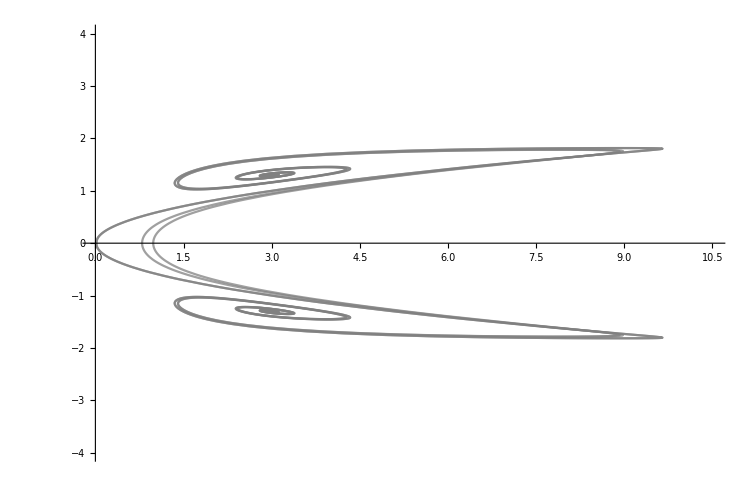

```mathematica
ParametricPlot[Evaluate[Table[{x1[t],y1[t]}/.sol[i],{i,1,6}], {t,-50,50},PlotStyle -> {{Gray, Opacity[0.75]}},PlotRange->{{0,10.5},{-4,4}}]]
```

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

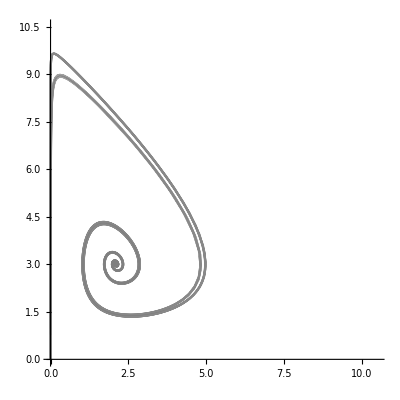

```mathematica
ParametricPlot[Evaluate[Table[{z1[t],x1[t]}/.sol[i],{i,1,6}], {t,-50,50},PlotStyle -> {{Gray, Opacity[0.75]}},PlotRange->{{0,10.5},{0,10.5}}]]
```

#### Fig 9 b

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1t:=x1'[t]==-3*y1[t]*x1[t]*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
de2t:=y1'[t]==-y1[t]^2-(1/6)*(x1[t]+z1[t]+3*wx*x1[t]+3*ϵ*x1[t]^2)
de3t:=z1'[t]==-3*y1[t]*z1[t]+ q*x1[t]*y1[t]*z1[t]
```

```mathematica
q=1;
wx=-0.6;
ϵ=-0.25;
```

```mathematica
traj[x0_,y0_,z0_]=NDSolve[{de1t,de2t,de3t, x1[0]==x0,y1[0]==y0,z1[0]==z0}, {x1,y1,z1},{t,-50,50}];
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[2,0.1,0.009];
sol[2]=traj[0.5,0.1,0.009];
sol[3]=traj[5,0.1,0.009];
sol[4]=traj[4,0.1,0.009];
sol[5]=traj[1,0.1,0.009];
```

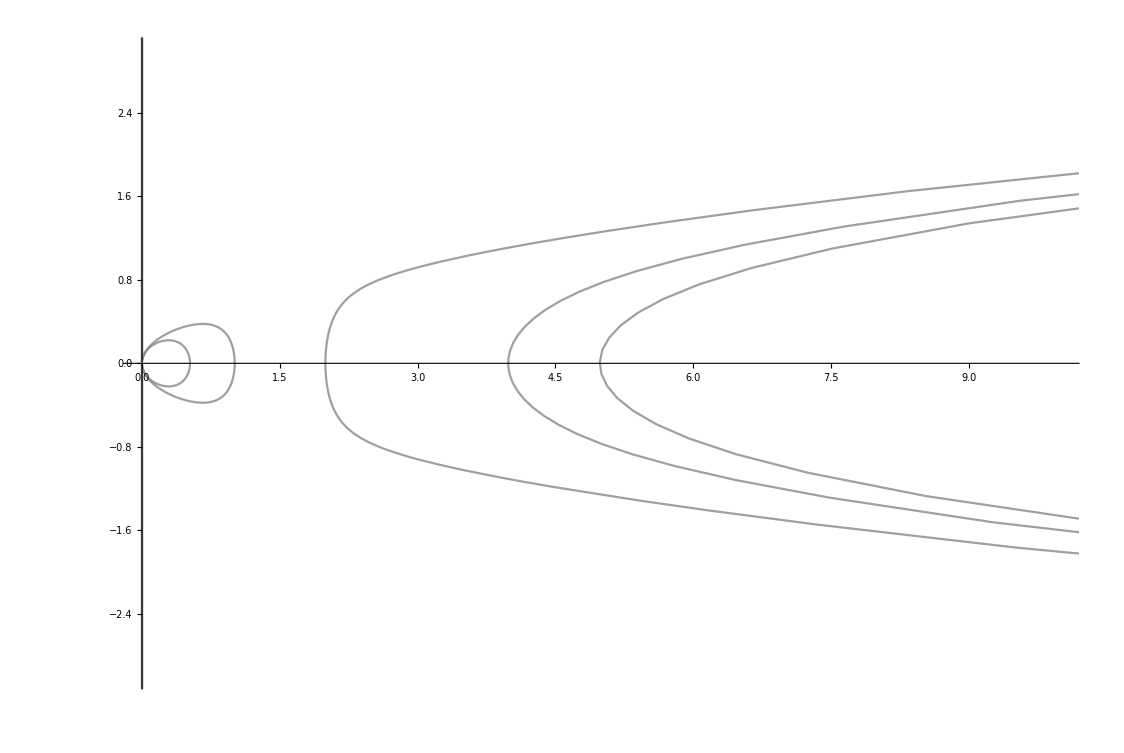

```mathematica
ParametricPlot[Evaluate[Table[{x1[t],y1[t]}/.sol[i],{i,1,5}], {t,-50,50},PlotStyle -> {{Gray, Opacity[0.75]}},PlotRange->{{0,10},{-3,3}}]]
```